```mathematica
Import["sin_1.png"]
```

Import::nffil: File sin_1.png not found during Import.

$Failed

```mathematica
SetDirectory[$UserDocumentsDirectory]
```

C:\Users\97587\Documents

```mathematica
file=FileNameJoin[{$InstallationDirectory,"Desktop","This PC","Documents","GitHub","WSS-Template","Final Project","Drafts","Images","Sin_1.png"}];
```

```mathematica
Import[file]
```

Import::nffil: File D:\Mathematica\Desktop\This PC\Documents\GitHub\WSS-Template\Final Project\Drafts\Images\Sin_1.png not found during Import.

$Failed

```mathematica
Directory[]
```

C:\Users\97587\Documents

```mathematica
SetDirectory["C:\\"]
```

C:\

```mathematica
file=FileNameJoin[{"Documents","GitHub","WSS-Template","Final Project","Drafts","Images","Sin_1.png"}]
```

```mathematica
"Documents\\GitHub\\WSS-Template\\Final Project\\Drafts\\Images\\Sin_1.png"
```

Documents\GitHub\WSS-Template\Final Project\Drafts\Images\Sin_1.png

```mathematica
Img=Import[file]
```

-Graphics-

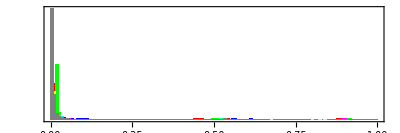

```mathematica
ImageHistogram[Img]
```

```mathematica
DominantColors[%]
```

{RGBColor[6.636694485562685*^-8, 6.636686583450336*^-8, 6.636681958909097*^-8, 0.],RGBColor[0.3999997979338314, 0.3999994754160956, 0.39999930595934846, 1.],RGBColor[0., 0.9999999225178172, 0., 1.]}

```mathematica
ColorQuantize[Img,{Black,White}]
```

-Graphics-

```mathematica
RemoveBackground[Img]
```

-Graphics-

```mathematica
ImageCases[Import[file],"Sin"]
```

ImageCases::nnlderr: An internal error occurred while loading a neural net. Please try again.

$Failed

```mathematica
image = -Graphics-;
```

```mathematica
ImageCases[image]
```

ImageCases::nnlderr: An internal error occurred while loading a neural net. Please try again.

$Failed

```mathematica
ImageCases[-Graphics-]
```

ImageCases::nnlderr: An internal error occurred while loading a neural net. Please try again.

$Failed